# The Social Leverage Effect

## Introduction

Here, we provide a brief description of the model, and the objective of this document. For a full description, see Supplementary Information.

### Model

Infinitely many actors and choosers engage in an infinitely repeated game. Choosers are short-run players.
Actors are long-run players, and are each characterized by a discount factor δ belonging to (0,1). δ is drawn at the birth, according to the population distribution of discount rates. An important parameter is μ, the mode of this distribution, which we refer to as the patience of the population.

In each round, actors each play one trust game with probability q, or the institution game with probability 1-q.
- Trust game: each actor plays with one chooser. First, the chooser can pay k to trust, in which case the actor gains r. If trusted, second, the actor can pay c1 to reciprocate, in which case the chooser earns back b>k (the other option is to cheat).
The actor’s behavior is observed with baseline probability p1 by future choosers.
- Institution game: every actor who drew the institution game c2 to contribute to the institution (the other option is to free-ride). Their behavior is observed with probability p2 by future choosers.

Actors are born with empty reputation. For each actor, choosers have access to one piece of information at best; the actor’s behavior in the previous stage, if any & observed. In other words, there are five possible reputations: empty, reciprocated, cheated, contributed, and free-rode.

We refer to reciprocating a partner’s trust as first-order cooperation, and contributing to the institution as second-order cooperation. We use the words cooperation and reciprocation interchangeably, as well as the words cheating and defection.

The institution incentivizes first-order cooperation, by: rewarding reciprocation by β, punishing cheating by γ, and increasing the probability of observation in the trust game by π1. These incentives go to the fraction q of trust games played that round. 

The total incentives produced by the institution are: q (  β + γ + c1 * π1) (a factor of conversion c1 is applied to π1).
The total contributions coming into the institution are: (1-q) f2 c2  --- where f2 measures the fraction of contributors among actors who face the institution game that round.
We assume that:
					ρ  * Total contributions  = Total contributions
			
ρ  is the efficiency of the institution. For every unit contributed to the institution, ρ units of incentives are created by the institution.
Taking into account the effects of the institution in equilibrium, when trusted, the signaler gains rc = r - c1 + β if she reciprocates, rd = r - γ if she cheats, and is subsequently observed with probability p1 = p1 + π1.

We assume that: 
		p2 ≥ p1  &  rd - rc ≥ c2

These conditions guarantee that, even after accounting for the effects of the institution, cooperation remains less likely to be observed, and more costly, than contribution to the institution---in an equilibrium in which reputation incentivizes both, contribution requires passing a lower bar (i.e. a threshold discount factor---see below and SI) than cooperation. In such an equilibrium, all cooperators contribute to the institution, but not all contributors can be expected to cooperation.

Parameters in bold are variables: they depend on the fraction f2 of contributors at the specific equilibrium, as well as the allocation between reward/punishment/monitoring performed by the institution. Below, we consider specific allocations, and obtain relevant variables by first computing f2 as a function of all parameters.

### Possible Perfect Bayesian Equilibria

0) There is always a trivial uncooperative Perfect Bayesian Equilibrium (from here one: PBE), whereby choosers never trust and actors never cooperate nor contribute. Below, we ignore the trivial equilibrium, and focus on the other two types of PBE, which are:

1) Non-institution equilibria, which are obtained when choosers trust given past cooperation (i.e. trust an actor’s who reputation is ‘reciprocated’), do not trust given past defection, and treat contribution and free-riding the same (e.g., do not trust given past contribution, and do not trust given past free-riding). Chooser equilibrium behavior given empty reputation is left free, and depends on the baseline probability of cooperation (see under). We denote θ the probability that choosers trust given empty reputation.
In such a case, reputation incentivizes first-order cooperation but not second-order cooperation: actors who pay to help a partner are more likely to be trusted in the future, and hence may earn a net benefit from doing so (depending on their time preferences); in contrast, it is always net costly to pay to contribute to the institution, since doing so will not lead to any later benefit. As a result, the institution is moot: it does not receive any contributions.

2) The institution equilibrium, which is obtained when choosers trust given past cooperation and given past contribution, and do not trust given defection or free-riding. Again, we denote θ the probability that choosers trust given empty reputation.
In such a case, reputation incentivizes both first- and second-order cooperation.

For every parameter values, we show that (see SI) there exists at best a unique institution equilibrium, which includes a unique value of θ. Actor equilibrium strategy is a reaction norm of the discount factor they are born with, which can be described by two threshold discount factors:
	- δ1 , the discount factor above which actors reciprocate a chooser’s trust
	- δ2, the discount factor above which actors contribute to the institution
Similarly, we show that there exists a unique baseline equilibrium for a given set of parameter values, which can be described by a unique θ and a unique δ1.

Below, we compare results (e.g., the level of cooperation obtained in that specific equilibrium):
- in the institution equilibrium, and
- in the non-institution equilibrium given that p2=0. We call this (specific case of a non-institution equilibrium) the baseline equilibrium. 

When p2=0, the institution equilibrium is impossible: second-order cooperation cannot be incentivized, because contributions are not observed by choosers. In addition, taking p2=0 provides a natural baseline for comparison: when p2=0, the institution game is simply ignored, and does not factor into an individual’s actor reputation. Actors start out with empty reputation, and may alternate with the reputation ‘reciprocated’ or ‘cheated’ depending on their behavior in the trust game. In contrast, when p2>0, actors obtain a bad reputation (meaning that they can be certain not to be trusted in the next round) each time the institution game is drawn, regardless of their behavior.

## General formula

Here, we provide a list of general formula, which will be used to calculate relevant values (e.g., the level of cooperation) in the baseline or the institution equilibria.

### Signaler threshold discount factors

#### For reciprocation (first-order cooperation)

In either the baseline or institution equilibrium, the threshold above which actors reciprocate a partner’s trust is:

```mathematica
Delta1[q_,rc_,rd_,p1_,θ_]:=(rd-rc)/ (p1 q ( rd -θ (rd-rc)))
```

δ1(θ) spans the interval [δ1(0) = (rd - rc ) / ( p1 q rd) , δ1(1) = (rd - rc) / ( p1 q rc) ]. The less often Choosers accept given null information, the more there is to be gained by achieving a good reputation; and the lower the bar above which Actors cooperate.
Note that we have written δ1(θ) as a function of the variables rc, rd, and p1. This expression is valid both for the baseline and the institution equilibria---although in the latter case, the final value is expected to be lower, thanks to the incentives produced by the institution.

In the absence of any institutional incentives (i.e. given β =γ =π1=0), we call δ1^b=δ1(0) = (c1) / (p1 q r) the difficulty of cooperation --- the minimum bar that must be surpassed for an actor to reciprocate (in particular, when δ1^b>1, no individual actor will reciprocate in the baseline equilibrium).

#### For contribution (second-order cooperation)

In the institution equilibrium, the threshold above which actors contribute to the institution is:

```mathematica
Delta2[q_,rd_,p1_,c2_,p2_,θ_]:=(c2)/(q(p2 rd - p1 θ c2))
```

Under our assumptions, 0 < δ2(θ) ≤ δ1(θ) : in the institution equilibrium, actors who reciprocate also contribute.

### Fraction of cooperators (first- and second-order)

We assume that discount factors are distributed according to a truncated normal distribution of mode μ and standard deviation σ.
In either the baseline or institution equilibrium, given threshold δ1, the fraction of cooperators f1 is equal to:

```mathematica
FractionDefectors[δ1_, μ_,σ_]:=CDF[TruncatedDistribution[{0,1},NormalDistribution[μ,σ]],δ1]
FractionCooperators[δ1_, μ_,σ_]:=1-FractionDefectors[δ1, μ,σ]
```

In the institution equilibrium, given threshold δ2, the fraction of contributors f2 is equal to:

```mathematica
FractionFreeRiders[δ2_, μ_,σ_]:=CDF[TruncatedDistribution[{0,1},NormalDistribution[μ,σ]],δ2]
FractionContributors[δ2_, μ_,σ_]:=1-FractionFreeRiders[δ2, μ,σ]
```

Under our assumptions, we have: 0 < f1 ≤ f2.

### Equilibrium conditions

#### Institution equilibrium

In the institution equilibrium, an actor who contributes must have a discount factor δ ≥ δ2. The probability P(R|C) that she reciprocates given that she contributes is then equal to:

```mathematica
ProbaReciprocatesGivenContributed[δ1_,δ2_, μ_,σ_]:=FractionCooperators[δ1,μ,σ]/FractionContributors[δ2,μ,σ]
```

When a chooser trusts an actor who contributed, she pays -k and earns back b with P(R|C). To obtain a PBE, we must then have k ≤ P(R|C) *b. In fact, we obtain the institution equilibrium iff (see SI):

```mathematica
PBEInstitution[δ1_,δ2_,k_,b_,μ_,σ_]:=(0<δ2<=δ1<1 )&& (k<=b*ProbaReciprocatesGivenContributed[δ1,δ2, μ,σ])
```

#### Baseline equilibrium

Under our hypotheses, the baseline equilibrium is obtained iff:

```mathematica
PBENoInstitution[δ1_]:=(0<δ1<1 )
```

### Average lifetime actor payoff

#### Value of good reputation

In a cooperative equilibrium (i.e. either the baseline equilibrium of the institution equilibrium), actors can alternate between good standing & bad standing, depending on their actions & chooser strategy (notably the value of θ). Let UG be the continuation payoff that an actor can expect when in good standing (when she is sure to be accepted by a chooser this round, were the trust game to be selected) and UB be her continuation payoff when in bad standing. We define the value of good reputation to be the difference: R = UG - UB. We show that R is a function of an individual’s discount factor δ, and that in a cooperative equilibrium, it is equal to:

```mathematica
R[q_,rc_,rd_,p1_,δ1_,θ_,δ_]:=If[δ<δ1, ( q rd)/(1+δ p1 q θ),(q rc)/(1-δ p1 q (1-θ))]
```

#### Average actor payoff in the baseline equilibrium

In the baseline equilibrium, starting from null reputation, an actor of discount factor δ can expect to earn average lifetime payoff (averaged over all rounds):

```mathematica
AverageActorPayoffNoInstitution[q_,rc_,rd_,p1_,δ1_,θ_,δ_]:=θ* R[q,rc,rd,p1,δ1,θ,δ]
```

Average Actor payoff in the institution equilibrium

In the institution equilibrium, starting from null reputation, an actor of discount factor δ can expect to earn average lifetime payoff (averaged over all rounds):

```mathematica
AverageActorPayoffInstitution[q_,rc_,rd_,p1_,c2_,p2_,δ1_,δ2_,θ_,δ_]:=If[δ< δ2, (1-(1-q) p2 δ )θ* R[q,rc,rd,p1,δ1,θ,δ],(1-q)(-c2)+(θ+(1-q) p2 δ(1-θ))* R[q,rc,rd,p1,δ1,θ,δ]]
```

### Steady state of the actor’s reputation

We note C1, D1, C2, D2, and E the five possible reputational states. An actor is in reputational state C1 (D1) if she cooperated (defected) the previous round and was observed. She is in reputational state C2 (D2) if she contributed (free-rode) the previous round and was observed. She is in reputational state E if her action in the previous round was not observed (and in the initial round).

Baseline equilibrium

In the baseline equilibrium,  there are two types of actors: High patience, who always cooperate, and Low patience, who always defect. Behavior in the institution game (i.e. not contributing) does not affect reputation since p2=0. Each type’s reputation follows a Markov process, whose steady state probabilities we give below.

High types alternate between reputations C1 and E. The steady state probabilities are:

```mathematica
PC1HighNoInstitution[q_,p1_,θ_]:=(q  θ p1)/(1-q(1-θ)p1)
PEHighNoInstitution[q_,p1_,θ_]:=1-PC1HighNoInstitution[q,p1,θ]
```

Low types alternate between reputations D1 and E. The steady state probabilities are:

```mathematica
PD1LowNoInstitution[q_,p1_,θ_]:=(q  θ p1)/(1+q θ p1)
PELowNoInstitution[q_,p1_,θ_]:=1-PD1LowNoInstitution[q,p1,θ]
```

Given a certain fraction f1 of high types, the probability that a chooser in the steady state faces an individual of reputation equal to E, C1, or D1 is:

```mathematica
PENoInstitution[f1_,q_,p1_,θ_]:= PEHighNoInstitution[q,p1,θ]*f1+PELowNoInstitution[q,p1,θ]*(1-f1)
PC1NoInstitution[f1_,q_,p1_,θ_]:= PC1HighNoInstitution[q,p1,θ]*f1+0
PD1NoInstitution[f1_,q_,p1_,θ_]:=0+PD1LowNoInstitution[q,p1,θ]*(1-f1)
```

#### Institution equilibrium

In the institution equilibrium, there are three types of actors: High patience, who always cooperate and contribute; Intermediate patience, who always defect and contribute; and Low patience, who always defect and free-ride. Each type’s reputation follows a Markov process, whose steady state probabilities we give below.

High types alternate between reputations C1, C2, and E. The steady state probabilities are:

```mathematica
PC1HighInstitution[q_,p1_,p2_,θ_]:=q p1((1-q)p2(1-θ)+ θ)/(1-q(1-θ)p1)
PC2HighInstitution[q_,p1_,p2_,θ_]:=(1-q)p2
PEHighInstitution[q_,p1_,p2_,θ_]:=1-PC1HighInstitution[q,p1,p2,θ]-PC2HighInstitution[q,p1,p2,θ]
```

Intermediate types alternate between reputations D1, C2, and E. The steady state probabilities are:

```mathematica
PD1IntermediateInstitution[q_,p1_,p2_,θ_]:=q p1((1-q)p2(1-θ)+ θ)/(1+q θ p1)
PC2IntermediateInstitution[q_,p1_,p2_,θ_]:=(1-q)p2
PEIntermediateInstitution[q_,p1_,p2_,θ_]:=1-PD1IntermediateInstitution[q,p1,p2,θ]-PC2IntermediateInstitution[q,p1,p2,θ]
```

Low types alternate between reputations D1, D2, and E. The steady state probabilities are:

```mathematica
PD1LowInstitution[q_,p1_,p2_,θ_]:=q θ p1(1-(1-q)p2)/(1+q θ p1)
PD2LowInstitution[q_,p1_,p2_,θ_]:=(1-q)p2
PELowInstitution[q_,p1_,p2_,θ_]:=1-PD1LowInstitution[q,p1,p2,θ]-PD2LowInstitution[q,p1,p2,θ]
```

Given a certain fraction f1 of high types, and a fraction f2-f1 of intermediate types (we note f2 the proportion of contributors, i.e. the proportion of intermediate or high types), the probability that a chooser in the steady state faces an individual of reputation equal to E, C1, D1, C2, or D2 is:

```mathematica
PEInstitution[f1_,f2_,q_,p1_,p2_,θ_]:= PEHighInstitution[q,p1,p2,θ]*f1+PEIntermediateInstitution[q,p1,p2,θ]*(f2-f1)+PELowInstitution[q,p1,p2,θ]*(1-f2)
PC1Institution[f1_,f2_,q_,p1_,p2_,θ_]:= PC1HighInstitution[q,p1,p2,θ]*f1+0+0
PD1Institution[f1_,f2_,q_,p1_,p2_,θ_]:=0+PD1IntermediateInstitution[q,p1,p2,θ]*(f2-f1)+PD1LowInstitution[q,p1,p2,θ]*(1-f2)
PC2Institution[f1_,f2_,q_,p1_,p2_,θ_]:=PC2HighInstitution[q,p1,p2,θ]*f1+PC2IntermediateInstitution[q,p1,p2,θ]*(f2-f1)+0
PD2Institution[f1_,f2_,q_,p1_,p2_,θ_]:=0+0+PD2LowInstitution[q,p1,p2,θ]*(1-f2)
```

### Level of cooperation in the steady state

#### Baseline equilibrium

Given a certain fraction f1 of high types, in the steady state, the probability that an actor of reputation E cooperates is equal to:

```mathematica
ProbaCooperateGivenEmptyNoInstitution[f1_,q_,p1_,θ_]:=
(PEHighNoInstitution[q,p1,θ]*f1)/PENoInstitution[f1,q,p1,θ]
```

This probability will be useful in determining the equilibrium value of θ below. The probability that an actor of reputation C1 (resp. D1) cooperates is equal to 1 (resp. 0).

Averaging over all possible reputations, we deduce that in the steady state, the probability that a randomly selected actor is trusted, and then cooperates is equal to (we call this measure the level of cooperation):

```mathematica
LevelCooperationNoInstitution[f1_,q_,p1_,θ_]:=
PENoInstitution[f1,q,p1,θ]*θ*ProbaCooperateGivenEmptyNoInstitution[f1,q,p1,θ]+PC1NoInstitution[f1,q,p1,θ]*1*1+0
```

#### Institution equilibrium

Given a certain fraction f1 of high types, and a fraction f2-f1 of intermediate types, with f2>f1>0, in the steady state, the probability that an actor of reputation E cooperates is equal to:

```mathematica
ProbaCooperateGivenEmptyInstitution[f1_,f2_,q_,p1_,p2_,θ_]:=
( PEHighInstitution[q,p1,p2,θ]*f1)/PEInstitution[f1,f2,q,p1,p2,θ]
```

This probability will be useful in determining the equilibrium value of θ below. The probability that an actor of reputation C1 (resp. D1) cooperates is equal to 1 (resp. 0).
The probability that an actor of reputation C2 (resp. D2) cooperates is equal to f1/f2 (resp. 0).

In the steady state, the probability that a randomly selected actor is trusted, and then cooperates is equal to:

```mathematica
LevelCooperationInstitution[f1_,f2_,q_,p1_,p2_,θ_]:=
PEInstitution[f1,f2,q,p1,p2,θ]*θ*ProbaCooperateGivenEmptyInstitution[f1,f2,q,p1,p2,θ]+PC1Institution[f1,f2,q,p1,p2,θ]*1*1+PC2Institution[f1,f2,q,p1,p2,θ]*1*f1/f2+0+0
```

### Chooser payoffs in the steady state

#### Baseline equilibrium

In the steady state, the expected payoff of a chooser who faces a randomly selected actor (assuming the trust game is drawn) is:

```mathematica
LongRunPayoffChooserNoInstitution[f1_,q_,p1_,k_,b_,θ_]:=
PC1NoInstitution[f1,q,p1,θ]*(b-k)+PENoInstitution[f1,q,p1,θ]*θ*(-k+ProbaCooperateGivenEmptyNoInstitution[f1,q,p1,θ]*b)
```

#### Institution equilibrium

In the steady state, the expected payoff of a chooser who faces a randomly selected actor (assuming the trust game is drawn) is:

```mathematica
LongRunPayoffChooserInstitution[f1_,f2_,q_,p1_,p2_,b_,k_,θ_]:=
PEInstitution[f1,f2,q,p1,p2,θ]*θ*(-k+ProbaCooperateGivenEmptyInstitution[f1,f2,q,p1,p2,θ]*b)+
PC1Institution[f1,f2,q,p1,p2,θ]*1*(-k+1*b)+
PC2Institution[f1,f2,q,p1,p2,θ]*1*(-k+f1/f2*b)
```

## Results

Here, we calculate and plot results in the baseline equilibrium, as well as in 4 examples of the institution equilibrium: respectively, when the institution allocates all incentives to rewarding cooperators, punishing defectors, increasing the probability of observation, and splits incentives between punishment and monitoring. To do so, we use the formulas from the previous section, and the general parameter values (and bisection method) introduced just below.
(Note: to obtain better resolution, increase PlotPoints and MaxRecursion in the DensityPlots below---as we do for the figures of the main text. The lower resolution plots computed here are the plots that figure in the Supplementary Information).

### Parameter values and bisection method (to run before any specific example)

#### Parameter values for first-order cooperation (and std. deviation)

We set our parameter values to be equal to:

```mathematica
q=0.5;
r=2;
p1=1/4;
σ=0.25;

b=1;
k=c1;
```

These parameter values are chosen so as to normalize the maximum expected actor payoff q * r = 1, and to leave plenty of “room” for improvement with the institution by setting p1=1/4.
As a consequence, the value of the difficulty of cooperation d is: 
		d = c1 / (p1 q r) = 4 * c1
Without an institution, the maximum attainable cost of cooperation is c1 = 1/4. Below, we vary the difficulty of cooperation between 0 and 4, while assuming that c1 =  p1 q r * d = d/4.
In addition, we assume that b = 1 = q*r, and that k=c1 --- thus assuming that the relative cost of trust for choosers is equal to the relative cost of cooperation for actors.

#### Parameter values for second-order cooperation

In addition, we assume that:

```mathematica
λ =3;
p2=λ*p1;
c2= c1 / λ;
```

Initially, second-order cooperation is three times as cheap as first-order cooperation, and three times as likely to be observed. (Once we compute the incentives produced by the institution, the difference in, e.g., the cost of first- and second-order cooperation, may shrink, but will remain positive in order to keep having c1 ≥ c2 and p1 ≥ p2.)

To compute results for an ‘efficient’ institution, we will set ρ=3. For an ‘inefficient’ institution, we will set ρ=1/3.

Bisection method

Note that in each case, the computationally expensive step is to calculate the equilibrium value of θ. To do so more rapidly, we use the bisection method (more detail in the “Baseline” subsection just below).

```mathematica
BisectionMethod[f_,{a_,b_},tol_:10^-4,maxIter_:1000]:=Module[{fa,fb,c,fc,iter=0,aLocal=a,bLocal=b},
fa=f[aLocal];
fb=f[bLocal];
(*Print["Initial a: ",aLocal,", f(a): ",fa];
Print["Initial b: ",bLocal,", f(b): ",fb];*)

While[iter<maxIter&&Abs[aLocal-bLocal]>tol,c=(aLocal+bLocal)/2;
fc=f[c];
(*Print["Iteration ",iter,": c = ",c,", f(c) = ",fc];*)

If[Abs[fc]<tol,Return[c]];
If[fa fc<0,(*if f(a) and f(c) have opposite signs*)bLocal=c;fb=fc,aLocal=c;fa=fc];
iter++];
(*Print["Final a: ",aLocal,", Final b: ",bLocal];*)

(aLocal+bLocal)/2]
```

### Baseline

#### Equilibrium value of θ

If a chooser trusts an actor of empty reputation E, he pays -k and earns b with probability P( C | E ), which we calculate in the steady state (see previous section). This probability is a function of θ, which itself indicates the level of trust by choosers given empty reputation in equilibrium.
To calculate θ despite the recursive nature of this problem, we exploit the fact that P( C | E ) is a strictly decreasing function of θ, and show that, in equilibrium, it must be equal to (see SI):

```mathematica
ThetaBaseline[q_,r_,c1_,p1_,k_,b_,μ_,σ_]:= 
Module[{δ1,f1,chooserPayoff},
δ1[θ_]:=Delta1[q,r-c1,r,p1,θ];
f1[θ_]:=FractionCooperators[δ1[θ],μ,σ];
chooserPayoff[θ_]:=-k+ProbaCooperateGivenEmptyNoInstitution[f1[θ],q,p1,θ]*b;
If[chooserPayoff[1]>0,1,
If[chooserPayoff[0]<0,0,
BisectionMethod[chooserPayoff,{0,1}]
]]]
```

#### Level of cooperation

The level of cooperation in the baseline equilibrium is:

```mathematica
LevelCooperationBaseline[q_,r_,c1_,p1_,k_,b_,μ_,σ_]:=
Module[{θ,δ1,f1},
θ=ThetaBaseline[q,r,c1,p1,k,b,μ,σ];
δ1=Delta1[q,r-c1,r,p1,θ];
f1=FractionCooperators[Delta1[q,r-c1,r,p1,θ],μ,σ];
If[PBENoInstitution[δ1],
LevelCooperationNoInstitution[f1,q,p1,θ]]]
```

When the patience of the population μ  varies between 0 and 1, and the difficulty of cooperation d varies between 0 and 4, the level of cooperation in the institution equilibrium is:

```mathematica
DensityPlot[LevelCooperationBaseline[q,r,d * p1 q r,p1,d * p1 q r,b,μ,σ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->2,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
ColorFunctionScaling->False,
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,1}}],
ColorFunction->(Blend[{White,Black},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Level of cooperation: No Institution",FontSize->17,Black]
]
```

-Graphics-

#### Payoffs

To calculate actor payoff, we compute the expected value of the average lifetime payoff of a randomly chosen actor (depending on the distribution of discount preferences, and therefore of behavior in the the trust game), normalized by dividing by q * r (which provides an upper bound on an actor’s payoff in a single round). We obtain:

```mathematica
ActorPayoffBaseline[q_,r_,c1_,p1_,k_,b_,μ_,σ_]:=
Module[{θ,δ1},
θ=ThetaBaseline[q,r,c1,p1,k,b,μ,σ];
δ1=Delta1[q,r-c1,r,p1,θ];
If[PBENoInstitution[δ1],If[θ>0,
(NExpectation[AverageActorPayoffNoInstitution[q,r-c1,r,p1,δ1,θ,δ],δ\[Distributed]TruncatedDistribution[{0, 1}, NormalDistribution[μ, σ]]])/(q * r)
,0]]]
```

To calculate chooser payoff, we assume that a trust game is drawn, and compute the expected payoff in the steady state of a chooser who faces a randomly drawn actor (depending once again on the distribution of discount preferences), normalized by dividing by b-k. We obtain:

```mathematica
ChooserPayoffBaseline[q_,r_,c1_,p1_,k_,b_,μ_,σ_]:=
Module[{θ,δ1,f1},
θ=ThetaBaseline[q,r,c1,p1,k,b,μ,σ];
δ1=Delta1[q,r-c1,r,p1,θ];
f1=FractionCooperators[Delta1[q,r-c1,r,p1,θ],μ,σ];
If[PBENoInstitution[δ1],
(LongRunPayoffChooserNoInstitution[f1,q,p1,k,b,θ])/(b-k)]]
```

We define the equilibrium payoff as the payoff of a randomly chosen individual---taking into account that choosers only play with probability q, while actors play with probability 1 (and hence weighing both previous payoffs accordingly).

```mathematica
PayoffBaseline[q_,r_,c1_,p1_,k_,b_,μ_,σ_]:=
q/(1+q)*ChooserPayoffBaseline[q,r,c1,p1,k,b,μ,σ]+
1/(1+q)*ActorPayoffBaseline[q,r,c1,p1,k,b,μ,σ]
```

### Example 1: rewarding institution (γ=π1=0)

#### Value of θ in equilibrium

Here, we consider an institution which neither punishes nor monitors (γ=π1=0), and instead allocates all multiplied contributions to rewarding cooperators, i.e. increasing the payoff of cooperators rc = r - c1 + β.
We assume that we always have (so that first-order cooperation remains more expensive than second-order cooperation even when accounting for the incentives produced by the institution):
	rd - rc  >= c2   <=>   rc <= r - c2
rc is then equal to:

```mathematica
PayoffCooperatorRewardingHypothesis[q_,r_,c1_,c2_,ρ_,f2_]:= Min[r-c1 + ρ(f2 c2)(1-q)/q,r-c2]
```

We check that chooser payoffs are a decreasing function of θ over our entire parameter region, using the below function and two region plots for the inefficient and efficient cases.

```mathematica
IsChooserPayoffDecreasingRewardingInstitution[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_,step_]:=
Module[{rc,δ1,δ2,f1,f2,chooserPayoff},
δ2[θ_]:=Delta2[q,r,p1,c2,p2,θ];
f2[θ_]:=FractionContributors[δ2[θ],μ,σ];
rc[θ_]:=PayoffCooperatorRewardingHypothesis[q,r,c1,c2,ρ,f2[θ]];
δ1[θ_]:=Delta1[q,rc[θ],r,p1,θ];
f1[θ_]:=FractionCooperators[δ1[θ],μ,σ];
chooserPayoff[θ_]:=-k+ProbaCooperateGivenEmptyInstitution[f1[θ],f2[θ],q,p1,p2,θ]*b;
numericalDerivative[θ_,h_]:=(chooserPayoff[θ+h]-chooserPayoff[θ])/h;
h=0.0001;
points=Range[0.01,0.99,step];
derivSigns=numericalDerivative[#,h]&/@points;
AllTrue[derivSigns,#<=0&]
]
```

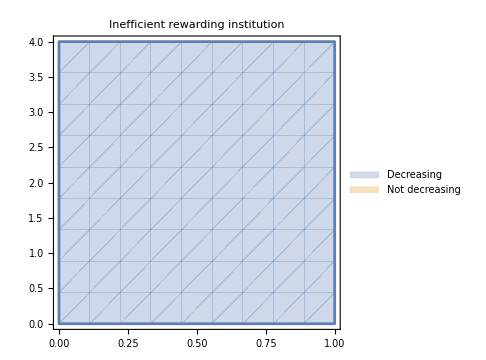

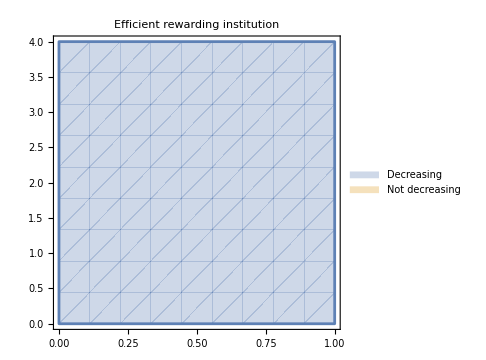

```mathematica
step=0.05;ρ=1/3;
RegionPlot[{IsChooserPayoffDecreasingRewardingInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step],Not[IsChooserPayoffDecreasingRewardingInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step]]},{μ,0,1},{d,0,4},
ImageSize->Medium,
MaxRecursion->1,
PlotPoints->10,
PlotRange->{{0,1},{0,4},{0,1}},
PlotLegends->{"Decreasing","Not decreasing"},
PlotLabel->"Inefficient rewarding institution"]
ρ=3;
RegionPlot[{IsChooserPayoffDecreasingRewardingInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step],Not[IsChooserPayoffDecreasingRewardingInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step]]},{μ,0,1},{d,0,4},
ImageSize->Medium,
MaxRecursion->1,
PlotPoints->10,
PlotRange->{{0,1},{0,4},{0,1}},
PlotLegends->{"Decreasing","Not decreasing"},
PlotLabel->"Efficient rewarding institution"]
```

Exploiting the fact that chooser payoffs are a decreasing function of θ in our parameter region, we show that the equilibrium value of θ verifies:

```mathematica
ThetaRewardingInstitution[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{rc,δ1,δ2,f1,f2,chooserPayoff},
δ2[θ_]:=Delta2[q,r,p1,c2,p2,θ];
f2[θ_]:=FractionContributors[δ2[θ],μ,σ];
rc[θ_]:=PayoffCooperatorRewardingHypothesis[q,r,c1,c2,ρ,f2[θ]];
δ1[θ_]:=Delta1[q,rc[θ],r,p1,θ];
f1[θ_]:=FractionCooperators[δ1[θ],μ,σ];
chooserPayoff[θ_]:=-k+ProbaCooperateGivenEmptyInstitution[f1[θ],f2[θ],q,p1,p2,θ]*b;
If[chooserPayoff[1]>0,1,
If[chooserPayoff[0]<0,0,
BisectionMethod[chooserPayoff,{0,1}]
]]]
```

#### Level of cooperation

In an institution equilibrium, the level of cooperation is:

```mathematica
LevelCooperationRewardingInstitution[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{θ,rc,δ1,δ2,f1,f2},
θ=ThetaRewardingInstitution[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ];
δ2=Delta2[q,r,p1,c2,p2,θ];
f2=FractionContributors[δ2,μ,σ];
rc=PayoffCooperatorRewardingHypothesis[q,r,c1,c2,ρ,f2];
δ1=Delta1[q,rc,r,p1,θ];
f1=FractionCooperators[δ1,μ,σ];
If[PBEInstitution[δ1,δ2,k,b,μ,σ],
LevelCooperationInstitution[f1,f2,q,p1,p2,θ]]]
```

In the case of an efficient institution (ρ=3), when the patience of the population μ varies between 0 and 1, and the difficulty of cooperation d varies between 0 and 4, the level of cooperation in the institution equilibrium is:

```mathematica
ρ=3
DensityPlot[LevelCooperationRewardingInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
ColorFunctionScaling->False,
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,1}}],
ColorFunction->(Blend[{White,Black},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Level of cooperation: Efficient Rewarding Institution",FontSize->17,Black]
]
```

3

-Graphics-

And in the case of an inefficient institution (ρ=1/3):

```mathematica
ρ=1/3
DensityPlot[LevelCooperationRewardingInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
ColorFunctionScaling->False,
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,1}}],
ColorFunction->(Blend[{White,Black},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Level of cooperation: Inefficient Rewarding Institution",FontSize->17,Black]
]
```

1/3

-Graphics-

### Example 2: monitoring institution (β=γ=0)

#### Value of θ in equilibrium

Here, we consider an institution which neither punishes nor rewards (γ=β=0), and instead allocates all multiplied contributions to monitoring the trust game, i.e. increasing the likelihood of the observation p1.
We assume that we always have (so that first-order cooperation remains less likely to be observed than second-order cooperation even when accounting for the incentives produced by the institution):
	p1 <= p2
p1 is then equal to:

```mathematica
ProbabilityObservationMonitoringHypothesis[q_,r_,c1_,p1_,c2_,p2_,ρ_,f2_]:=Min[p2 , p1 +(ρ  f2  c2/c1)* (1-q)/q ]
```

We deduce, as a function of θ:

```mathematica
ProbabilityObservationMonitoringStep2[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_,θ_]:=ProbabilityObservationMonitoringHypothesis[q,r,c1,p1,c2,p2,ρ,FractionContributors[Delta2[q,r,p1,c2,p2,θ],μ,σ]]
```

We check that chooser payoffs are a decreasing function of θ over our entire parameter region, using the below function and two region plots for the inefficient and efficient cases.

```mathematica
IsChooserPayoffDecreasingMonitoringInstitution[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_,step_]:=
Module[{P1,δ1,δ2,f1,f2,chooserPayoff},
P1[θ_]:=ProbabilityObservationMonitoringStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
δ1[θ_]:=Delta1[q,r-c1,r,P1[θ],θ];
f1[θ_]:=FractionCooperators[δ1[θ],μ,σ];
δ2[θ_]:=Delta2[q,r,P1[θ],c2,p2,θ];
f2[θ_]:=FractionContributors[δ2[θ],μ,σ];
chooserPayoff[θ_]:=-k+ProbaCooperateGivenEmptyInstitution[f1[θ],f2[θ],q,P1[θ],p2,θ]*b;
numericalDerivative[θ_,h_]:=(chooserPayoff[θ+h]-chooserPayoff[θ])/h;
h=0.0001;
points=Range[0.01,0.99,step];
derivSigns=numericalDerivative[#,h]&/@points;
AllTrue[derivSigns,#<=0&]
]
```

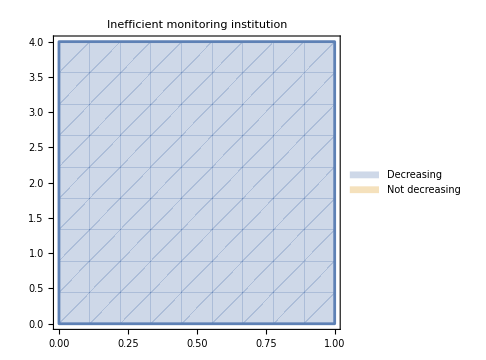

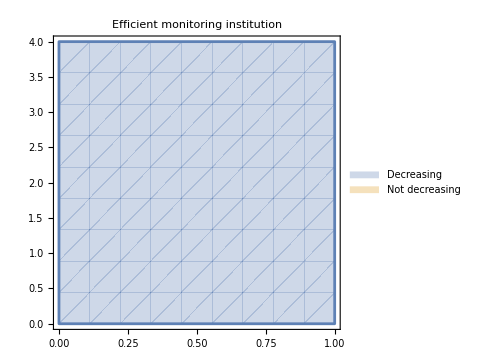

```mathematica
step=0.05;ρ=1/3;
RegionPlot[{IsChooserPayoffDecreasingMonitoringInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step],Not[IsChooserPayoffDecreasingMonitoringInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step]]},{μ,0,1},{d,0,4},
ImageSize->Medium,
MaxRecursion->1,
PlotPoints->10,
PlotRange->{{0,1},{0,4},{0,1}},
PlotLegends->{"Decreasing","Not decreasing"},
PlotLabel->"Inefficient monitoring institution"]
ρ=3;
RegionPlot[{IsChooserPayoffDecreasingMonitoringInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step],Not[IsChooserPayoffDecreasingMonitoringInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step]]},{μ,0,1},{d,0,4},
ImageSize->Medium,
MaxRecursion->1,
PlotPoints->10,
PlotRange->{{0,1},{0,4},{0,1}},
PlotLegends->{"Decreasing","Not decreasing"},
PlotLabel->"Efficient monitoring institution"]
```

Exploiting the fact that chooser payoffs are a decreasing function of θ in our parameter region, we show that the equilibrium value of θ verifies:

```mathematica
ThetaMonitoringInstitution[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{P1,δ1,δ2,f1,f2,chooserPayoff},
P1[θ_]:=ProbabilityObservationMonitoringStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
δ1[θ_]:=Delta1[q,r-c1,r,P1[θ],θ];
f1[θ_]:=FractionCooperators[δ1[θ],μ,σ];
δ2[θ_]:=Delta2[q,r,P1[θ],c2,p2,θ];
f2[θ_]:=FractionContributors[δ2[θ],μ,σ];
chooserPayoff[θ_]:=-k+ProbaCooperateGivenEmptyInstitution[f1[θ],f2[θ],q,P1[θ],p2,θ]*b;
If[chooserPayoff[1]>0,1,
If[chooserPayoff[0]<0,0,
BisectionMethod[chooserPayoff,{0,1}]
]]]
```

#### Level of cooperation

In an institution equilibrium, the level of cooperation is:

```mathematica
LevelCooperationMonitoringInstitution[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{θ,P1,δ1,δ2,f1,f2},
θ=ThetaMonitoringInstitution[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ];
P1=ProbabilityObservationMonitoringStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
δ1=Delta1[q,r-c1,r,P1,θ];
δ2=Delta2[q,r,P1,c2,p2,θ];
f1=FractionCooperators[δ1,μ,σ];
f2=FractionContributors[δ2,μ,σ];
If[PBEInstitution[δ1,δ2,k,b,μ,σ],
LevelCooperationInstitution[f1,f2,q,P1,p2,θ]]]
```

In the case of an efficient institution (ρ=3), when the patience of the population μ varies between 0 and 1, and the difficulty of cooperation d varies between 0 and 4, the level of cooperation in the institution equilibrium is:

```mathematica
ρ=3
DensityPlot[LevelCooperationMonitoringInstitution[q,r,d* p1 q r,p1,d*p1 q r/λ,λ*p1,d* p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
ColorFunctionScaling->False,
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,1}}],
ColorFunction->(Blend[{White,Black},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Level of cooperation: Efficient Monitoring Institution",FontSize->17,Black]
]
```

3

-Graphics-

And for an inefficient institution (ρ=1/3):

```mathematica
ρ=1/3
DensityPlot[LevelCooperationMonitoringInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,λ*p1,d* p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
ColorFunctionScaling->False,
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,1}}],
ColorFunction->(Blend[{White,Black},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Level of cooperation: Inefficient Monitoring Institution",FontSize->17,Black]
]
```

1/3

-Graphics-

### Example 3: punishing institution (β=π1=0)

#### Value of θ in equilibrium

Here, we consider an institution which neither rewards nor monitors (γ=β=0), and instead allocates all multiplied contributions to punishing cheaters in the trust game, i.e. decreasing the payoff of defectors rd = r -γ.
We assume that we always have (so that first-order cooperation remains more expensive than second-order cooperation even when accounting for the incentives produced by the institution):
	rd - rc >=  c2  <=>  rd >= r - c1 + c2
rd is then equal to:

```mathematica
PayoffDefectorPunishingHypothesis[q_,r_,c1_,c2_,ρ_,f2_]:= Max[r- ρ(f2 c2)(1-q)/q,r-c1 +c2]
```

We deduce, as a function of θ:

```mathematica
PayoffDefectorPunishingStep2[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_,θ_]:=PayoffDefectorPunishingHypothesis[q,r,c1,c2,ρ,FractionContributors[Delta2[q,r,p1,c2,p2,θ],μ,σ]]
```

We check that chooser payoffs are a decreasing function of θ over our entire parameter region, using the below function and two region plots for the inefficient and efficient cases.

```mathematica
IsChooserPayoffDecreasingPunishingInstitution[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_,step_]:=
Module[{rd,δ1,δ2,f1,f2,chooserPayoff},
rd[θ_]:=PayoffDefectorPunishingStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
δ1[θ_]:=Delta1[q,r-c1,rd[θ],p1,θ];
f1[θ_]:=FractionCooperators[δ1[θ],μ,σ];
δ2[θ_]:=Delta2[q,rd[θ],p1,c2,p2,θ];
f2[θ_]:=FractionContributors[δ2[θ],μ,σ];
chooserPayoff[θ_]:=-k+ProbaCooperateGivenEmptyInstitution[f1[θ],f2[θ],q,p1,p2,θ]*b;
numericalDerivative[θ_,h_]:=(chooserPayoff[θ+h]-chooserPayoff[θ])/h;
h=0.0001;
points=Range[0.01,0.99,step];
derivSigns=numericalDerivative[#,h]&/@points;
AllTrue[derivSigns,#<=0&]
]
```

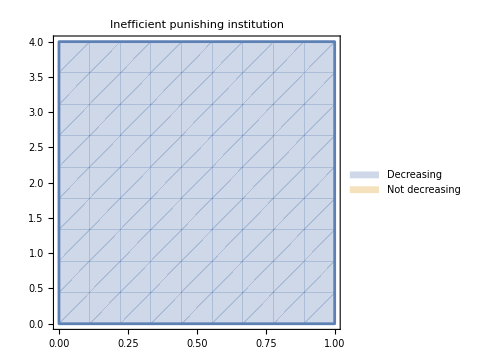

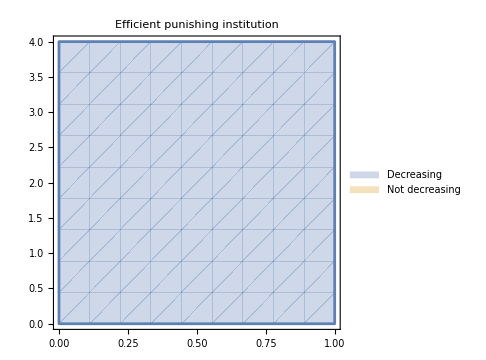

```mathematica
step=0.05;ρ=1/3;
RegionPlot[{IsChooserPayoffDecreasingPunishingInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step],Not[IsChooserPayoffDecreasing[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step]]},{μ,0,1},{d,0,4},
ImageSize->Medium,
MaxRecursion->1,
PlotPoints->10,
PlotRange->{{0,1},{0,4},{0,1}},
PlotLegends->{"Decreasing","Not decreasing"},
PlotLabel->"Inefficient punishing institution"]
ρ=3;
RegionPlot[{IsChooserPayoffDecreasingPunishingInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step],Not[IsChooserPayoffDecreasing[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step]]},{μ,0,1},{d,0,4},
ImageSize->Medium,
MaxRecursion->1,
PlotPoints->10,
PlotRange->{{0,1},{0,4},{0,1}},
PlotLegends->{"Decreasing","Not decreasing"},
PlotLabel->"Efficient punishing institution"]
```

Exploiting the fact that chooser payoffs are a decreasing function of θ in our parameter region, we show that the equilibrium value of θ verifies:

```mathematica
ThetaPunishingInstitution[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{rd,δ1,δ2,f1,f2,chooserPayoff},
rd[θ_]:=PayoffDefectorPunishingStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
δ1[θ_]:=Delta1[q,r-c1,rd[θ],p1,θ];
f1[θ_]:=FractionCooperators[δ1[θ],μ,σ];
δ2[θ_]:=Delta2[q,rd[θ],p1,c2,p2,θ];
f2[θ_]:=FractionContributors[δ2[θ],μ,σ];
chooserPayoff[θ_]:=-k+ProbaCooperateGivenEmptyInstitution[f1[θ],f2[θ],q,p1,p2,θ]*b;
If[chooserPayoff[1]>0,1,
If[chooserPayoff[0]<0,0,
BisectionMethod[chooserPayoff,{0,1}]
]]]
```

#### Level of cooperation

In an institution equilibrium, the level of cooperation is:

```mathematica
LevelCooperationPunishingInstitution[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{θ,rd,δ1,δ2,f1,f2},
θ=ThetaPunishingInstitution[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ];
rd=PayoffDefectorPunishingStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
δ1=Delta1[q,r-c1,rd,p1,θ];
δ2=Delta2[q,rd,p1,c2,p2,θ];
f1=FractionCooperators[δ1,μ,σ];
f2=FractionContributors[δ2,μ,σ];
If[PBEInstitution[δ1,δ2,k,b,μ,σ],
LevelCooperationInstitution[f1,f2,q,p1,p2,θ]]]
```

In the case of an efficient institution (ρ=3), when the patience of the population μ varies between 0 and 1, and the difficulty of cooperation d varies between 0 and 4, the level of cooperation in the institution equilibrium is:

```mathematica
ρ=3
DensityPlot[LevelCooperationPunishingInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,λ*p1,d * p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
ColorFunctionScaling->False,
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,1}}],
ColorFunction->(Blend[{White,Black},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Level of cooperation: Efficient Punishing Institution",FontSize->17,Black]
]
```

3

-Graphics-

And in the case of an inefficient institution (ρ=1/3):

```mathematica
ρ=1/3
DensityPlot[LevelCooperationPunishingInstitution[q,r,d * p1 q r,p1,d*p1 q r/λ,λ*p1,d * p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
ColorFunctionScaling->False,
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,1}}],
ColorFunction->(Blend[{White,Black},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Level of cooperation: Inefficient Punishing Institution",FontSize->17,Black]
]
```

1/3

-Graphics-

### Example 4: main text example---equal allocations between punishment and monitoring (α=π1; β=0)

#### Value of θ in equilibrium

Here, we consider an institution which does not reward cooperators (β=0), and instead allocates multiplied contributions equally between punishing and monitoring, i.e. to:
- decreasing the payoff of defectors rd = r - γ
- and increasing the probability of observation p1 = p1 + π1,
- with γ = c1 * π1 (since we weighed the increase in observability π1 by c1 in the equation giving the total amount of incentives produced by the institution).
We assume that we always have:
		rd - rc >=  c2  <=>  rd >= r - c1 + c2
and		p1 <= p1
Under these assumption, second-order cooperation remains cheaper and more likely to be observed than first-order cooperation even after accounting for the effect of the institution.
rd and p1 are then equal to:

```mathematica
PayoffDefectorMainHypothesis[q_,r_,c1_,c2_,ρ_,f2_]:= Max[r- 1/2*ρ(f2 c2)(1-q)/q,r-c1 +c2]
ProbabilityObservationMainHypothesis[q_,r_,c1_,p1_,c2_,p2_,ρ_,f2_]:=Min[p2 , p1 +1/2*ρ( f2 c2 / c1)  (1-q)/q ]
```

We deduce, as a function of θ:

```mathematica
PayoffDefectorMainStep2[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_,θ_]:=PayoffDefectorMainHypothesis[q,r,c1,c2,ρ,FractionContributors[Delta2[q,r,p1,c2,p2,θ],μ,σ]]
ProbabilityObservationMainStep2[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_,θ_]:=ProbabilityObservationMainHypothesis[q,r,c1,p1,c2,p2,ρ,FractionContributors[Delta2[q,r,p1,c2,p2,θ],μ,σ]]
```

We check that chooser payoffs are a decreasing function of θ over our entire parameter region, using the below function and two region plots for the inefficient and efficient cases.

```mathematica
IsChooserPayoffDecreasingMainExample[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_,step_]:=
Module[{rd,P1,δ1,δ2,f1,f2,chooserPayoff},
rd[θ_]:=PayoffDefectorMainStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];P1[θ_]:=ProbabilityObservationMainStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
δ1[θ_]:=Delta1[q,r-c1,rd[θ],P1[θ],θ];
f1[θ_]:=FractionCooperators[δ1[θ],μ,σ];
δ2[θ_]:=Delta2[q,rd[θ],P1[θ],c2,p2,θ];
f2[θ_]:=FractionContributors[δ2[θ],μ,σ];
chooserPayoff[θ_]:=-k+ProbaCooperateGivenEmptyInstitution[f1[θ],f2[θ],q,P1[θ],p2,θ]*b;
numericalDerivative[θ_,h_]:=(chooserPayoff[θ+h]-chooserPayoff[θ])/h;
h=0.0001;
points=Range[0.01,0.99,step];
derivSigns=numericalDerivative[#,h]&/@points;
AllTrue[derivSigns,#<=0&]
]
```

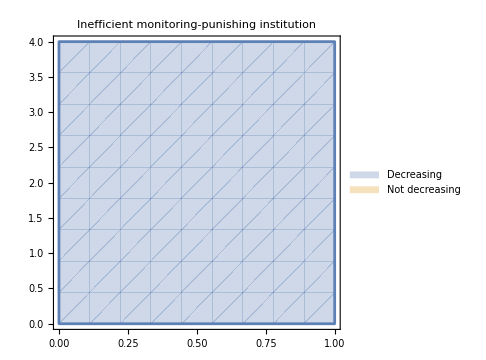

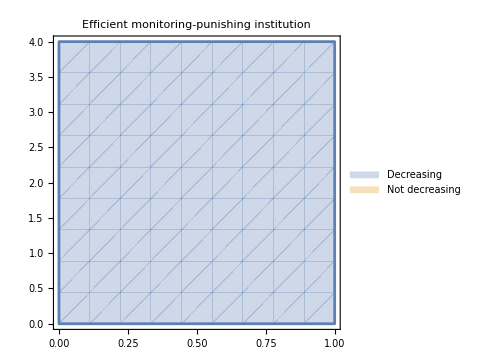

```mathematica
step=0.05;ρ=1/3;
RegionPlot[{IsChooserPayoffDecreasingMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step],Not[IsChooserPayoffDecreasingMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step]]},{μ,0,1},{d,0,4},
ImageSize->Medium,
MaxRecursion->1,
PlotPoints->10,
PlotRange->{{0,1},{0,4},{0,1}},
PlotLegends->{"Decreasing","Not decreasing"},
PlotLabel->"Inefficient monitoring-punishing institution"]
ρ=3;
RegionPlot[{IsChooserPayoffDecreasingMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step],Not[IsChooserPayoffDecreasingMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,p2,d * p1 q r,b,μ,σ,ρ,step]]},{μ,0,1},{d,0,4},
ImageSize->Medium,
MaxRecursion->1,
PlotPoints->10,
PlotRange->{{0,1},{0,4},{0,1}},
PlotLegends->{"Decreasing","Not decreasing"},
PlotLabel->"Efficient monitoring-punishing institution"]
```

Exploiting the fact that chooser payoffs are a decreasing function of θ in our parameter region, we show that the equilibrium value of θ verifies:

```mathematica
ThetaMainExample[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{rd,P1,δ1,δ2,f1,f2,chooserPayoff},
rd[θ_]:=PayoffDefectorMainStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];P1[θ_]:=ProbabilityObservationMainStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
δ1[θ_]:=Delta1[q,r-c1,rd[θ],P1[θ],θ];
f1[θ_]:=FractionCooperators[δ1[θ],μ,σ];
δ2[θ_]:=Delta2[q,rd[θ],P1[θ],c2,p2,θ];
f2[θ_]:=FractionContributors[δ2[θ],μ,σ];
chooserPayoff[θ_]:=-k+ProbaCooperateGivenEmptyInstitution[f1[θ],f2[θ],q,P1[θ],p2,θ]*b;
If[chooserPayoff[1]>0,1,
If[chooserPayoff[0]<0,0,
BisectionMethod[chooserPayoff,{0,1}]
]]]
```

#### Level of cooperation

In an institution equilibrium, the level of cooperation (defined as the rate of cooperation in the first round see above) is given by:

```mathematica
LevelCooperationMainExample[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{θ,rd,P1,δ1,δ2,f1,f2},
θ=ThetaMainExample[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ];
rd=PayoffDefectorMainStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
P1=ProbabilityObservationMainStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
δ1=Delta1[q,r-c1,rd,P1,θ];
δ2=Delta2[q,rd,P1,c2,p2,θ];
f1=FractionCooperators[δ1,μ,σ];
f2=FractionContributors[δ2,μ,σ];
If[PBEInstitution[δ1,δ2,k,b,μ,σ],
LevelCooperationInstitution[f1,f2,q,P1,p2,θ]]]
```

In the case of an efficient institution (ρ=3), when the patience of the population μ varies between 0 and 1, and the difficulty of cooperation d varies between 0 and 4, the level of cooperation in the institution equilibrium is:
(Note: to obtain the images used in the main text, set PlotPoints at 100, and use the options Frame->None, Axes->False, PlotRangePadding->None, PlotRange->{{0,1},{0,3.25},{0,1}})

```mathematica
ρ=3
DensityPlot[LevelCooperationMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,λ*p1,d * p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
ColorFunctionScaling->False,
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,1}}],
ColorFunction->(Blend[{White,Black},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Level of cooperation: Efficient Monitoring-Punishing Institution",FontSize->17,Black]
]
```

3

-Graphics-

And in the case of an inefficient institution (ρ=1/3):

```mathematica
ρ=1/3
DensityPlot[LevelCooperationMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,λ*p1,d * p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
ColorFunctionScaling->False,
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,1}}],
ColorFunction->(Blend[{White,Black},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Level of cooperation: Inefficient Monitoring-Punishing Institution",FontSize->17,Black]
]
```

1/3

-Graphics-

#### Expected Payoffs

As in the baseline, to calculate actor payoff, we compute the expected value of the average lifetime payoff of a randomly chosen actor (depending on the distribution of discount preferences, and therefore of behavior in the the trust game), normalized by dividing by q * r (which provides an upper bound on an actor’s payoff in a single round). And, to calculate chooser payoff, we assume that a trust game is drawn, and compute the expected payoff in the steady state of a chooser who faces a randomly drawn actor (depending once again on the distribution of discount preferences), normalized by dividing by b-k. The expected payoff is the weighted sum of the two, with weight q for the chooser payoff, and 1 for the actor payoff (since choosers play with probability in any given round, and actors with probability 1).
We obtain:

```mathematica
ActorPayoffMainExample[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{θ,rd,P1,δ1,δ2},
θ=ThetaMainExample[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ];
rd=PayoffDefectorMainStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
P1=ProbabilityObservationMainStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
δ1=Delta1[q,r-c1,rd,P1,θ];
δ2=Delta2[q,rd,P1,c2,p2,θ];
If[PBEInstitution[δ1,δ2,k,b,μ,σ],(NExpectation[AverageActorPayoffInstitution[q,r-c1,rd,P1,c2,p2,δ1,δ2,θ,δ],δ\[Distributed]TruncatedDistribution[{0, 1}, NormalDistribution[μ, σ]]])/(q*r)]
]

ChooserPayoffMainExample[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{θ,rd,P1,δ1,δ2,f1,f2},
θ=ThetaMainExample[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ];
rd=PayoffDefectorMainStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
P1=ProbabilityObservationMainStep2[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ,θ];
δ1=Delta1[q,r-c1,rd,P1,θ];
δ2=Delta2[q,rd,P1,c2,p2,θ];
f1=FractionCooperators[δ1,μ,σ];
f2=FractionContributors[δ2,μ,σ];
If[PBEInstitution[δ1,δ2,k,b,μ,σ],
LongRunPayoffChooserInstitution[f1,f2,q,P1,p2,b,k,θ]/(b-k)]]

PayoffMainExample[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
(q*ChooserPayoffMainExample[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ]+1*ActorPayoffMainExample[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ])/(1+q)
```

### Comparison between example 4 and the baseline case

#### Increase in the level of cooperation

When the monitoring-punishing institution is a PBE, the level of cooperation is always greater than the level of cooperation in the baseline equilibrium (provided the latter exists). 
Subtracting, we deduce the increase in cooperation provided by the main institution studied:

```mathematica
IncreaseCooperationMainExample[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{main,baseline,result},
main=LevelCooperationMainExample[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ];
baseline=LevelCooperationBaseline[q,r,c1,p1,k,b,μ,σ];
result=Which[NumericQ[main]&&NumericQ[baseline],main-baseline,NumericQ[main],main,True,None];
result]
```

In the case of an efficient institution (ρ=3), when the patience of the population μ varies between 0 and 1, and the difficulty of cooperation d varies between 0 and 4, the increase in cooperation is:

```mathematica
ρ=3
DensityPlot[IncreaseCooperationMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,λ*p1,d*p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
ColorFunctionScaling->False,
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,1}}],
ColorFunction->(Blend[{White,Black},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Increase in cooperation: Efficient Monitoring-Punishing Institution",FontSize->17,Black]
]
```

3

-Graphics-

With an inefficient institution (ρ=1/3) we obtain:

```mathematica
ρ=1/3
DensityPlot[IncreaseCooperationMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,λ*p1,d*p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
ColorFunctionScaling->False,
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,1}}],
ColorFunction->(Blend[{White,Black},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Increase in cooperation: Inefficient Monitoring-Punishing Institution",FontSize->17,Black]
]
```

1/3

-Graphics-

#### Change in expected payoffs

When the monitoring-punishing institution is a PBE, the expected chooser payoff is always greater than in the baseline equilibrium (provided the latter exists), since actors’ incentive to reciprocate increases. However, the expected actor payoff may be smaller, since paying for the institution may be inefficient if actors were already very likely to cooperate without an institution.

We define three functions, in order to separate between increases and decreases (since decreases are much smaller; see below):

```mathematica
DifferencePayoffMainExample[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{main,baseline,result},
main=PayoffMainExample[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ];
baseline=PayoffBaseline[q,r,c1,p1,k,b,μ,σ];
result=Which[NumericQ[main]&&NumericQ[baseline],main-baseline,NumericQ[main],main,True,None];
result]

PositiveDifferencePayoffMainExample[q_,args___]:=With[{val=DifferencePayoffMainExample[q,args]},If[val>=0,val,Null]]
NegativeDifferencePayoffMainExample[q_,args___]:=With[{val=DifferencePayoffMainExample[q,args]},If[val<0,val,Null]]
```

We compare between the efficient institution and the baseline case.
As visible below, with our chosen parameters, the decrease in total payoff is always small---at most, payoffs suffer a decrease barely above 0.6%, for large values of μ and small values of d:

```mathematica
ρ=3;
better=DensityPlot[PositiveDifferencePayoffMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,λ*p1,d * p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
Mesh->None,
PlotLegends->BarLegend[{Automatic, {0,1}}],
ColorFunction->(Blend[{White,Blue},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Change in Payoff: Efficient Monitoring-Punishing Institution",FontSize->17,Black],
ColorFunctionScaling->False
];
```

```mathematica
worse =DensityPlot[-NegativeDifferencePayoffMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,λ*p1,d * p1 q r,b,μ,σ,ρ],{μ,0.5,1},{d,0,0.5},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->30,
PlotRange->{{0,1},{0,4},{0,1}},
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,0.006}}],
ColorFunction->(Blend[{White,Red},Rescale[#,{0,0.006}]]&),
ColorFunctionScaling->False
];
```

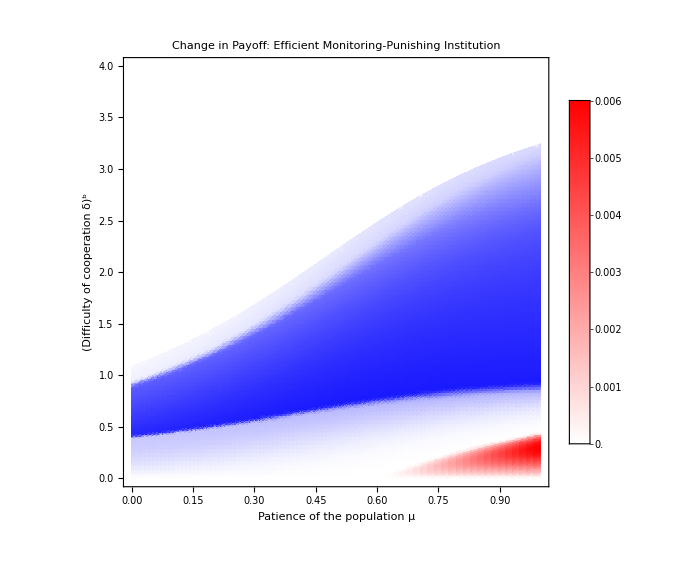

```mathematica
Show[{better,worse}]
```

#### Change in actor and chooser payoffs

To more visually see their separate contributions, here, we distinguish changes in actor and chooser payoffs. Recall that chooser payoffs can only increase due to an institution being stabilized.

```mathematica
IncreaseChooserPayoffMainExample[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{main,baseline,result},
main=ChooserPayoffMainExample[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ];
baseline=ChooserPayoffBaseline[q,r,c1,p1,k,b,μ,σ];
result=Which[NumericQ[main]&&NumericQ[baseline],main-baseline,NumericQ[main],main,True,None];
result]

DifferenceActorPayoffMainExample[q_,r_,c1_,p1_,c2_,p2_,k_,b_,μ_,σ_,ρ_]:=
Module[{main,baseline,result},
main=ActorPayoffMainExample[q,r,c1,p1,c2,p2,k,b,μ,σ,ρ];
baseline=ActorPayoffBaseline[q,r,c1,p1,k,b,μ,σ];
result=Which[NumericQ[main]&&NumericQ[baseline],main-baseline,NumericQ[main],main,True,None];
result]
PositiveDifferenceActorPayoffMainExample[q_,args___]:=With[{val=DifferenceActorPayoffMainExample[q,args]},If[val>=0,val,Null]]
NegativeDifferenceActorPayoffMainExample[q_,args___]:=With[{val=DifferenceActorPayoffMainExample[q,args]},If[val<0,val,Null]]
```

In the case of an efficient institution, when the patience of the population μ varies between 0 and 1, and the difficulty of cooperation d varies between 0 and 4, the increase in chooser payoffs is:

3

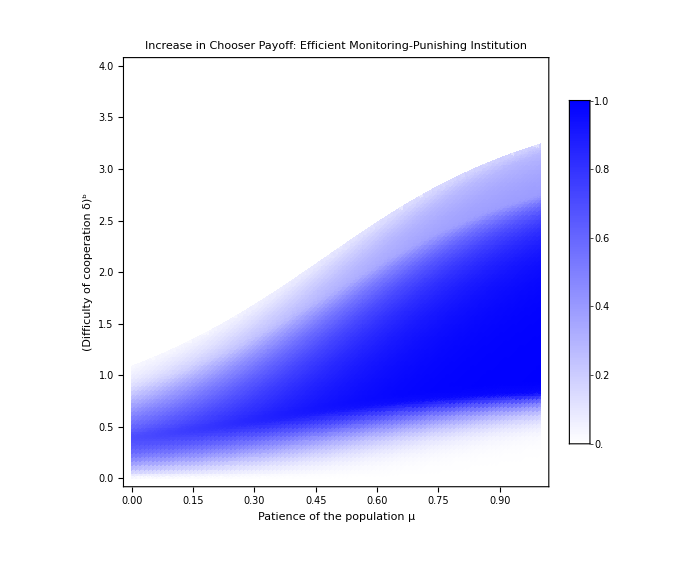

$Aborted

```mathematica
ρ=3
diffchooser=DensityPlot[IncreaseChooserPayoffMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,λ*p1,d * p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,4},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
Mesh->None,
PlotLegends->BarLegend[{Automatic, {0,1}}],
ColorFunction->(Blend[{White,Blue},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Increase in Chooser Payoff: Efficient Monitoring-Punishing Institution",FontSize->17,Black],
ColorFunctionScaling->False
]
```

In the case of an efficient institution, when the patience of the population μ varies between 0 and 1, and the difficulty of cooperation d varies between 0 and 4, the change in actor payoffs is:

```mathematica
ρ=3;
betterAct=DensityPlot[PositiveDifferenceActorPayoffMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,λ*p1,d * p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0.25,3.25},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->100,
PlotRange->{{0,1},{0,4},{0,1}},
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,1}}],
ColorFunction->(Blend[{White,Blue},#]&),
FrameLabel->{Style["Patience of the population μ",FontSize->13,Black],Style[Superscript["Difficulty of cooperation δ","b"],FontSize->13,Black]},
PlotLabel->Style["Change in Actor Payoff: Efficient Monitoring-Punishing Institution",FontSize->17,Black],
ColorFunctionScaling->False
];
```

```mathematica
worseAct =DensityPlot[-NegativeDifferenceActorPayoffMainExample[q,r,d * p1 q r,p1,d*p1 q r/λ,λ*p1,d * p1 q r,b,μ,σ,ρ],{μ,0,1},{d,0,1},
ImageSize->Large,
MaxRecursion->1,
Exclusions->None,
PlotPoints->60,
PlotRange->{{0,1},{0,4},{0,1}},
Mesh->None,
PlotLegends->BarLegend[{Automatic,{0,0.05}}],
ColorFunction->(Blend[{White,Red},Rescale[#,{0,0.05}]]&),
ColorFunctionScaling->False
];
```

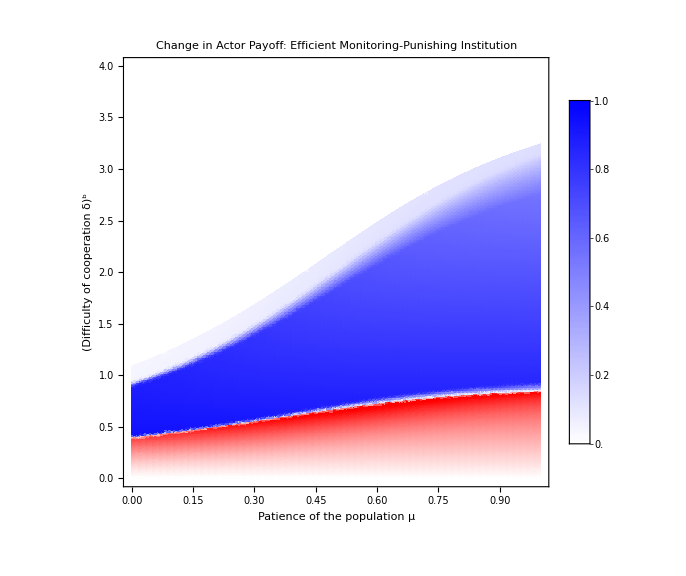

```mathematica
Show[{betterAct,worseAct}]
```